### Wprowadzenie wartości dla gęstości ziarenek piasku ( "ρ" ), czasu zderzenia ziaren piasku z metalem ( "Δt" ), kątów jakie tworzą wektory prędkości z normalna do powierzchni metalu przed ( "α" ) i po zderzeniu ( "β_1","β_2" ) i prędkości ziaren piasku ( "v" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
ρ=2.62×10^3;          (* kg/m^3 *)
```

```mathematica
Δt=1×10^-3;           (* s *)
```

```mathematica
α=45;                           (* deg *)
```

```mathematica
β1=45;                       (* deg *)
```

```mathematica
β2=30;                       (* deg *)
```

```mathematica
v=100;                           (* m/s *)
```

### Wprowadzenie wzorów na powierzchnie styku ziaren piasku z metalem ( "S" ) oraz na objętość ziaren piasku ( "V" ) i ich masę ( "m" ). Symbol ("r") oznacza promień ziaren.

```mathematica
S=π×r^2;
V=4/3×π×r^3;
m =ρ×V;
```

### Wprowadzenie wzorów na składowe normalne wektorów prędkości przed zderzeniem ( "v_pn" ) i po zderzeniu ( "v_kn" ). Symbol "v" oznacza długość wektora prędkości.

```mathematica
vpn=v×cos(α °);
vkn=0.6×v×cos(β °);
```

### Obliczenie składowych normalnych pędu ziarenek piasku przed zderzeniem z metalem ( "p_pn" ) i po zderzeniu ( "p_kn" ) oraz przyrostu pędu ziarenek ( "Δp_n" ).

```mathematica
ppn=-m×vpn;
pkn=m×vkn;
Δpn=pkn-ppn;
```

### Obliczenie składowej normalnej siły wywieranej przez ziarna na metal ( "F_n" ). Symbol "Δt" oznacza czas trwania zderzenia.

```mathematica
Fn=Δpn/Δt;
```

### Obliczenie ciśnienia wywieranego przez ziarna piasku na powierzchnię metalu ( "P" ).

```mathematica
P=Fn/S;
```

### Sporządzenie wykresu obrazującego zależność ciśnienia wywieranego przez ziarna piasku na powierzchnię metalu od promienia ziaren ( "r" ) dla kata β_1 = 45°.

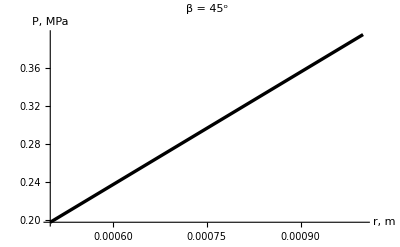

```mathematica
rys1=Plot[P×10^-6/.β->β1,{r,0.5×10^-3,1.0×10^-3},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     β  = 45^o    ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->{Black,Thickness[0.006]},AxesLabel->{"r, m","P,  MPa"}]
```

### Sporządzenie wykresu obrazującego zależność ciśnienia wywieranego przez ziarna piasku na powierzchnię metalu od promienia ziaren ( "r" ) dla kata β_2 = 30°.

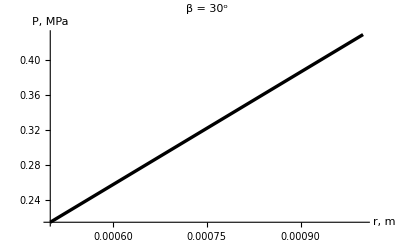

```mathematica
rys2=Plot[P×10^-6/.β->β2,{r,0.5×10^-3,1.0×10^-3},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     β  = 30^o   ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->{Black,Thickness[0.006]},AxesLabel->{"r, m","P,  MPa"}]
```